## init

```mathematica
SetOptions[#,
AxesStyle->Directive[Black,AbsoluteThickness[0.9]],
LabelStyle->Directive[Black,FontFamily->"CMU Serif",FontSize->16],
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[0.9]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[0.9],FontFamily->"CMU Serif",FontSize->13,FontSlant->Plain],
PlotRangePadding->{None,Automatic},
ImageSize->400
]&/@{Plot,LogPlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot,ListLinePlot};
```

```mathematica
SetOptions[#,
FrameStyle->Directive[Black,AbsoluteThickness[0.9]]
]&/@{Framed};
```

```mathematica
Attributes[myStyle]={Listable};
SetAttributes[myStyle,HoldAllComplete];
myStyle[form_,others___]:=Style[TraditionalForm[HoldForm[form]],others,FontFamily->"CMU Serif"];
```

## Converter

```mathematica
$Assumptions={GeV>0&&eV>0};
eV=1;
GeV=10^9 eV;
MeV=10^6 eV;
keV=10^3 eV;
(*eV=10^-9 GeV;*)
cm=(5.0677307165483375*^13)/GeV;
meter=100cm;
km=1000meter;
AU=149597870700meter;
sec=(1.5192674479961274*^24)/GeV;
kg=5.609588606807705*^26 GeV;
gram=10^-3 kg;
Kelvin=8.617333262000001*^-14 GeV;
joule=kg meter^2/sec^2;
GNewton=6.67430×10^−11 meter^3 kg^−1sec^−2;
```

```mathematica
CommonRules={
e->√(4π α),
α->1/137,
me->511keV,
mp->0.938272GeV,
mn->0.939565GeV,
amu->0.931494GeV,
Mpl->1.22*^19GeV,
ρDM->0.3 GeV/cm^3,
vDM->10^-3
};

Tesla=kg/(Ampere sec^2)/.Ampere->1/(1.602176634×10^−19)e/sec//.CommonRules;
```

## FormFactor ball

```mathematica
formFactorSphere[q_,R_,xi_]:=
1/(((4π)/3 R^3)^2)((8 π^2 xi^3 (3 xi (-3+q^2 xi^2) (R+q^2 R xi^2)^2+4 (R+q^2 R xi^2)^3+3 xi^3 (5-10 q^2 xi^2+q^4 xi^4)))/(3 (1+q^2 xi^2)^5)+1/(q (1+q^2 xi^2)^5)8 ⅇ^(-(2 R)/xi) π^2 xi^3 (q xi ((-3+q^2 xi^2) (R+q^2 R xi^2)^2+8 R xi (-1+q^4 xi^4)-xi^2 (5-10 q^2 xi^2+q^4 xi^4)) Cos[2 q R]+(-xi^2+10 q^2 xi^4-5 q^4 xi^6+(-1+3 q^2 xi^2) (R+q^2 R xi^2)^2-2 R (xi-5 q^2 xi^3-5 q^4 xi^5+q^6 xi^7)) Sin[2 q R]))
```

```mathematica
With[{q=100,xi=0.01,R=(1/((4π)/3)1)^(1/3)},
{
1/(((4π)/3 R^3)^2)(32 π^2)/3(R^3 xi^3)/((1+q^2 xi^2)^2),
formFactorSphere[q,R,xi]
}
]
```

{6.28319×10^-6,6.20721×10^-6}

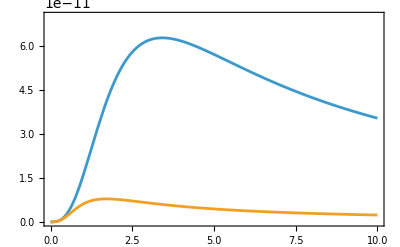

```mathematica
V=1cm^3;
RBall=(1/((4π)/3)V)^(1/3);
q1=0.1eV;
q2=0.2eV;
Plot[{formFactorSphere[q1,RBall,ξinμm 10^-6 meter],formFactorSphere[q2,RBall,ξinμm 10^-6 meter]},{ξinμm,0,10},PlotRange->{0,7*^-11}]//Quiet
```

## FormFactor cube

```mathematica
funcube[qx_,qy_,qz_,dx_,dy_,dz_,xi_]:=E^(ⅈ (qx dx+qy dy+qz dz))E^(-√(dx^2+dy^2+dz^2)/xi);
```

```mathematica
With[{qx=0,qy=0,qz=100,xi=0.01,Lx=1,Ly=1,Lz=1},
1/(Lx  Ly Lz)^2 NIntegrate[funcube[qx,qy,qz,dx,dy,dz,xi](Lx-Abs[dx])(Ly-Abs[dy])(Lz-Abs[dz]),{dx,-Lx,Lx},{dy,-Ly,Ly},{dz,-Lz,Lz}]
]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

6.21108×10^-6

```mathematica
With[{qx=0,qy=0,qz=30,xi=0.01,Lx=1,Ly=1,Lz=1},
1/(Lx  Ly Lz)NIntegrate[funcube[qx,qy,qz,dx,dy,dz,xi](Lx-Abs[dx])(Ly-Abs[dy])(Lz-Abs[dz]),{dx,-Lx,Lx},{dy,-Ly,Ly},{dz,-Lz,Lz},MaxRecursion->50]
]
```

0.0000203201

```mathematica
formFactorCube[qx_?NumericQ,qy_?NumericQ,qz_?NumericQ,LCube_?NumericQ,ξ_?NumericQ]:=1/((LCube^3)^2)NIntegrate[funcube[qx,qy,qz,dx,dy,dz,ξ](LCube-Abs[dx])(LCube-Abs[dy])(LCube-Abs[dz]),{dx,-LCube,LCube},{dy,-LCube,LCube},{dz,-LCube,LCube}];
```

```mathematica
ξinμmList=Subdivide[0.5,10,30];
qineVList=10^Subdivide[-2,0,30];
```

## Figure of ξ

```mathematica
LCube=V^(1/3);
formFactorCubeq1List=ParallelTable[{ξinμm,formFactorCube[0,0,q1,LCube,ξinμm*10^-6 meter]//Quiet},{ξinμm,ξinμmList}]//Chop[#,10^-14]&;
```

```mathematica
formFactorCubeq2List=ParallelTable[{ξinμm,formFactorCube[0,0,q2,LCube,ξinμm*10^-6 meter]//Quiet},{ξinμm,ξinμmList}]//Chop[#,10^-13]&;
```

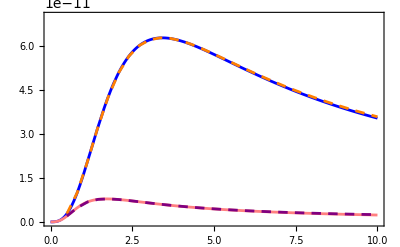

```mathematica
Show[
Plot[{formFactorSphere[q1,RBall,ξinμm 10^-6 meter],formFactorSphere[q2,RBall,ξinμm 10^-6 meter]},{ξinμm,0,10},PlotRange->{0,7*^-11},PlotStyle->{Directive[Blue],Directive[Pink]}]//Quiet,
ListPlot[{formFactorCubeq1List,formFactorCubeq2List},Joined->True,PlotStyle->{Directive[Orange,Dashing[{r,0.03-r}]/.r->0.017],Directive[Purple,Dashing[{r,0.03-r}]/.r->0.017],Opacity[1]}]
]
```

```mathematica
<<MaTeX`;
```

```mathematica
frameLable=MaTeX[#,FontSize->15]&/@{"\\xi \, [ \\mathrm{\\mu m} ]","|F(\\mathbf{q})|^2"};
legendLable=MaTeX/@{"\\text{ball}","\\text{cube}"};
parameterLable=MaTeX["
			 \\begin{aligned}
				 \\overline{\\delta n^2} &= \\bar{n}^2 \\\\
				 V &= 1 \, \\mathrm{cm}^{3} \\\\
				 q &= 0.1 \, \\mathrm{eV}
			 \\end{aligned}
			"];
legendLable2=MaTeX["\\xi = \\sqrt{3} \, q^{-1}"];
```

```mathematica
myColor1=RGBColor["#1E6BE8"]
myColor2=RGBColor["#ff7f0e"]
myColor3=RGBColor["#E5A84B"]
myColor4=RGBColor["#5DA39D"]
myColor5=RGBColor["#9d7fa9"]
```

RGBColor[0.11764705882352941, 0.4196078431372549, 0.9098039215686274]

RGBColor[1., 0.4980392156862745, 0.054901960784313725]

RGBColor[0.8980392156862745, 0.6588235294117647, 0.29411764705882354]

RGBColor[0.36470588235294116, 0.6392156862745098, 0.615686274509804]

RGBColor[0.615686274509804, 0.4980392156862745, 0.6627450980392157]

```mathematica
Show[
Plot[{formFactorSphere[q1,RBall,ξinμm 10^-6 meter]},{ξinμm,0,10},
PlotRange->{0,7*^-11},
PlotStyle->{Directive[myColor2]},
FrameLabel->frameLable
]//Quiet,
ListPlot[{formFactorCubeq1List},Joined->True,PlotStyle->{Directive[myColor1,Dashing[{r,0.03-r}]/.r->0.015,AbsoluteThickness[2.5]]}
],
Epilog->{
Inset[
LineLegend[{Directive[myColor2],Directive[myColor1,Dashing[{r,0.03-r}]/.r->0.015,AbsoluteThickness[2.5]]},
legendLable,
LegendMarkerSize->{{35,5}}(*,Spacings->0.3*)
],
Scaled[{0.7,0.02}],{Right,Bottom}
],
Inset[parameterLable,Scaled[{0.95,0.05}],{Right,Bottom}],
{Gray,Dotted,Line[{{√3 q1^-1/(10^-6 meter),0},{√3 q1^-1/(10^-6 meter),10^-10}}]},
Inset[Rotate[legendLable2,π/2],{1.05 √3 q1^-1/(10^-6 meter),2*^-11},{Left,Bottom}]
}
]
```

-Graphics-

## Figure of q

```mathematica
LCube=V^(1/3);
ξ1=2*^-6meter;
formFactorCubeξ1List=ParallelTable[{qineV,formFactorCube[0,0,qineV eV,LCube,ξ1]//Quiet},{qineV,qineVList}]//Chop[#,10^-14]&;
```

```mathematica
formFactorCubeξ1List//N
```

{{0.01,9.84095×10^-11+1.50079×10^-11 ⅈ},{0.0116591,9.76946×10^-11+1.73921×10^-11 ⅈ},{0.0135936,9.67354×10^-11+2.0112×10^-11 ⅈ},{0.0158489,9.54538×10^-11+2.31904×10^-11 ⅈ},{0.0184785,1.87504×10^-10},{0.0215443,1.83022×10^-10},{0.0251189,1.77183×10^-10},{0.0292864,1.69682×10^-10},{0.0341455,1.60227×10^-10},{0.0398107,1.48592×10^-10},{0.0464159,1.34703×10^-10},{0.054117,1.18743×10^-10},{0.0630957,1.01227×10^-10},{0.0735642,8.30154×10^-11},{0.0857696,6.5205×10^-11},{0.1,4.89116×10^-11},{0.116591,3.50077×10^-11},{0.135936,2.39378×10^-11},{0.158489,1.56877×10^-11},{0.184785,9.89903×10^-12},{0.215443,6.04652×10^-12},{0.251189,3.59492×10^-12},{0.292864,2.09118×10^-12},{0.341455,1.19566×10^-12},{0.398107,6.74561×10^-13},{0.464159,3.76713×10^-13},{0.54117,2.08767×10^-13},{0.630957,1.15044×10^-13},{0.735642,6.31518×10^-14},{0.857696,3.45663×10^-14},{1.,1.8887×10^-14}}

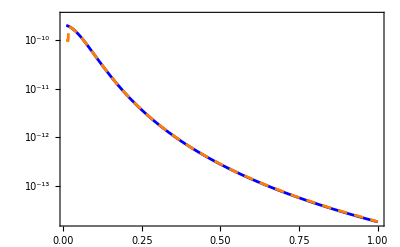

```mathematica
Show[
LogPlot[formFactorSphere[qineV eV,RBall,ξ1],{qineV,0.01,1},PlotRange->{0,30*^-11},PlotStyle->{Directive[Blue]}]//Quiet,
ListLogPlot[Re@formFactorCubeξ1List,Joined->True,PlotStyle->{Directive[Orange,Dashing[{r,0.03-r}]/.r->0.017],Directive[Purple,Dashing[{r,0.03-r}]/.r->0.017],Opacity[1]}]
]
```